# Sorting Networks

## Demonstrating the similarity between Bubble and Insertion Sorts.

Aviv Elazar-Mittelman

Sorting Networks are a type of oblivious comparison-based algorithm, which means that for all inputs of the same size, a constant number of comparisons is used. They are useful for building GPUs, as they can be easily parallelized and stacked together with minimal modifications to compare larger and larger numbers.

Here is an example of what a sorting network looks like:

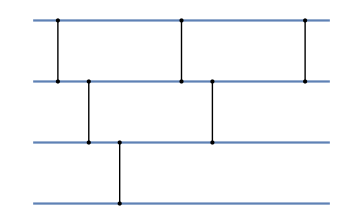

-Graphics-

Each blue line represents an input. Numbers enter the network from the left and exit (hopefully sorted) from the right. The vertical lines with dots at each end are called Comparators, and they compare and swap values of the two lines they are connected to. If the number in the top line is bigger than the number in the bottom line, then the values are swapped, otherwise the values pass through.

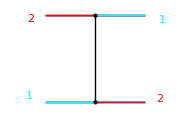
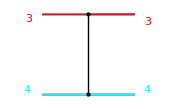

-Graphics- -Graphics-

Since Sorting Networks are comparison-based sorting algorithms, they suffer from the comparison lower bound of O(n log(n)). To find the number of comparisons that a sorting network uses, simply count the number of comparators. The example above is an Bubble Sorting Network, which is modeled after the classic Bubble Sort algorithm, an O(n^2) algorithm, for n inputs. A Bubble Sorting Network always performs (n(n-1))/2 comparisons. For the 4-input network above, 6 comparisons are used. It is called a bubble sorting network, because it tries to “bubble” down the largest value every iteration until the entire network is sorted.

This bubbling effect can be seen in this example, sorting the numbers 4,1,2,3:

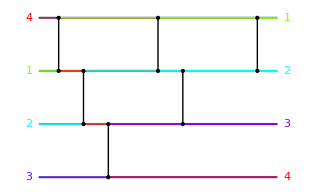

-Graphics-

Taking a look at the first comparator, we see that 4 is larger than 3, so the two values must be swapped. Since 4 is larger than the rest of the inputs, it will always be swapped, “bubbling” it down to the bottom. Since the largest value has now reached the bottom, it is sorted, and there is no point wasting an extra comparison to check that its still sorted, so we reduce the number of comparisons by 1 and bubble the next largest number to the bottom.

Another type of sorting network is based on the Insertion Sort algorithm. Here is an example 4-input network:

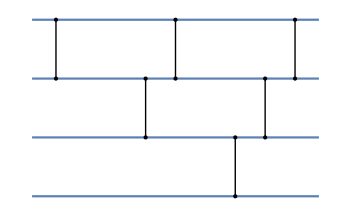

-Graphics-

This network attempts to “insert” the next value in the correct position among already sorted numbers. Unlike normal insertion sort, all comparisons are mandatory, which means that it has the same number of comparisons as a Bubble Sorting Network ((n(n-1))/2).

Here is the same example list as above but using an Insertion Sorting Network of size 4:

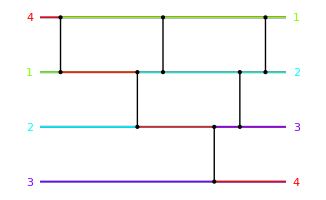

-Graphics-

In the first comparison, 4 and 1 are swapped like in bubble sort, however unlike bubble sort, we are finished with the first “stack” of comparisons. The network works by pulling a new element in each stack and moving it to the correct position in the sorted subsection.

Notice that the stacks of Bubble Sort and Insertion Sort are incredibly similar, the main difference being that Bubble Sort is left-aligned, and Insertion Sort is right-aligned. This is because we are suffering from the limitation of sorting 1 element at a time, so comparators cannot overlap, so we have to choose between the two. However, if we decide to move to a system with multiple processors, we can calculate comparisons on different lines at the same time (in parallel).

Here is an example of a Parallel Bubble Sorting network:

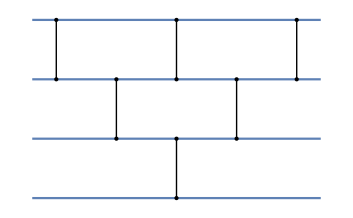

-Graphics-

As you can see, the third and fourth comparators occur at the same time, since they operate on different sets of wires. We achieve this by simply shifting the workload of the stacks so that they interleave with the other stacks.

Now, here is an example of a Parallel Insertion Sorting network:

-Graphics-

As you can see, they are identical. Don’t be fooled by the spacing between the comparators. This is just a visualization of what a network would look like. In reality, the comparators would be much closer together, and the parallel nature would allow for faster computations, as more instructions can be jammed together in a smaller time frame, compared to the sequential networks above.

With those explanations out of the way, you can now play with the model below.

```mathematica
(*Function that generates graphics for Comparators.*)
Connector[a_, b_, lcol_,dcol_]:={lcol, PointSize[Large], Line[{a,b}],dcol, Point[a], Point[b]}
Connector[a_,b_,col_]:=Connector[a,b,col,col]
Connector[a_,b_]:=Connector[a,b,Black,Black]
ActiveConnector[a_,b_]:=Connector[a,b,Red,Red]
```

```mathematica
(*Function that generates a stack of comparators at a certain x position for a specific sorting network type.*)
ConnectorStack[opt_,top_,height_,w_,spos_]:=
Module[{mod,space,result = {}, count = 0, i},
mod = Switch[opt,"Bubble",height,"Insertion",top-height, "Parallel",height];
space = Switch[opt,"Bubble",w,"Insertion",-w, "Parallel",.5];
For [i=top-1, i≥top-mod, i--,
result = Append[result,Connector[{spos+count space, i},{spos+count space, i-1}]];
count = count + 1
];
result
]
```

```mathematica
(*Function that generates all stacks for a specific sorting network.*)
ConnectorLines[opt_,n_,w_] :=
Module[{option,size = n, width = w,result = {},space = w/n,outer=n-1, i},
For[i=1, i<n,i++,
result = Append[result,ConnectorStack[opt,n,n-i, w, i-1]]
];
result
]
```

```mathematica
(*Function that generates graphics for a list of elements.*)
LabelGen[lst_, height_, loc_, cols_]:=
Module[{results = {},colors = {}, count = 1, currColor},
For[i=height-1, i ≥ 0, i--,
If[Length[cols]>0, currColor = cols[[count]],currColor = RandomColor[]];
AppendTo[colors,currColor];
AppendTo[results,Text[Style[lst[[count]],currColor, Large],{loc,i}]];
count++
];
{results,colors}
]
LabelGen[lst_,height_,loc_]:=LabelGen[lst,height,loc,{}]
```

```mathematica
(*Function that performs Bubble Sort on a list of elements. While sorting, the function also creates the graphics for the wires to indicate which value is currently passing through which wire.*)
BubbleSort[l_,c_,len_,w_]:=
Module[{lst = l,cols=c,i,j,count, steps = {{l,c}}, lines = {Thick}, xpos = 0, to},
count = len-1;
For[i=1, i≤len,i++,AppendTo[lines,{cols[[i]],Line[{{-.2,count},{len-1.8,count}}]}];count = count-1];
For[i=1,i≤len,i++,
count = len-1;
xpos = i-1;
For[j=1,j≤len-i,j++,
If[lst [[j]] > lst[[j+1]], lst[[{j,j+1}]] = lst[[{j+1,j}]]; cols[[{j,j+1}]] = cols[[{j+1,j}]]];
AppendTo[steps,{lst,cols}];
to = len-1.8;
AppendTo[lines,{cols[[j]],Line[{{xpos,count},{to,count}}]}];
AppendTo[lines,{cols[[j+1]],Line[{{xpos,count-1},{to,count-1}}]}];
xpos = xpos + w;
count = count-1
]
];
{lst,cols,steps, lines}
]
```

```mathematica
(*Function that performs Insertion Sort on a list of elements. Unlike normal insertion sort, all comparisons are mandatory, so we swap elements immediately rather than finding the correct positon first. While sorting, the function also creates the graphics for the wires to indicate which value is currently passing through which wire.*)
InsertionSort[l_,c_,len_,w_]:=
Module[{lst = l,cols=c,i,j,count, steps = {{l,c}}, lines = {Thick}, xpos = 0, to, key, keyC},
count = len-1;
For[i=1, i≤len,i++,AppendTo[lines,{cols[[i]],Line[{{-.2,count},{len-1.8,count}}]}];count = count-1];

For[i=2, i<=len, i++,
j=i;
count = len-1;
xpos = (i-2)(1-w);
While[j> 1&&lst[[j]]<lst[[j-1]],
lst[[{j,j-1}]]=lst[[{j-1,j}]];
cols[[{j,j-1}]]=cols[[{j-1,j}]];


AppendTo[steps,{lst,cols}];
to = len-1.8;
AppendTo[lines,{cols[[j]],Line[{{xpos,len-j},{to,len-j}}]}];
AppendTo[lines,{cols[[j-1]],Line[{{xpos,len-j+1},{to,len-j+1}}]}];


xpos = xpos + w;
count = count-1;
j = j-1;
]
];
{lst,cols,steps, lines}
]
```

```mathematica
(*Wrapper function for sorts that calls the correct sorting function. I use a trick to create the parallel network. Since I designed the network to have each stack occur in increments of 1 on the x-axis, we can create a parallel network by telling the stack builder to use a padding of .5 on either side of the comparator. This has the effect of generating the proper image.*)
SortSort[mode_,lst_,c_,len_,w_]:=Switch[mode,"Bubble",BubbleSort[lst,c,len,w], "Parallel",BubbleSort[lst,c,len,.5], "Insertion", InsertionSort[lst,c,len,w]]
```

```mathematica
(*Manipulate which calls all of the functions and plots the Sorting Network. A Sorting Network is constructed to fit the number of elements provided. If the sort checkbox is selected, The sorting process is shown. If the boring checkbox is selected, boring colors are used in the sorting process. The user can switch between the networks and observe the differences for the same list of elements.*)
Manipulate[
With[{values=Flatten@ToExpression@StringSplit[list,","]},
If[Length[values]==0,"Please enter a list of numbers.",
With[{colors = If[boring==False,Table[Hue[x],{x,0,1,1/(Length[values])}],Table[Gray, Length[values]]]},
With[{init= LabelGen[values,Length[values], -.3, colors], len = Length[values]},
With[{sorted = SortSort[mode,values,init[[2]],len, 1/len]},
With[{end = LabelGen[sorted[[1]],Length[values],len-1.7, sorted[[2]]]},
Show[
Plot[
Table[
y, {y,0,len-1}
],
{x,-.2,len-1.8}, Axes->False, ImageSize->Large,Epilog-> {ConnectorLines[mode,len, 1/len]}
(*set width to .2 for sequential, and .5 for parallel.*)
],
If[sort,Graphics[{init[[1]], end[[1]]}],Graphics[]],
If[sort,Graphics[{sorted[[4]]}],Graphics[]],
PlotRange-> Automatic
]
]
]
]
]
]
],
{list, "6,3,9,4,1", InputField[#,String]&},
{mode, {"Bubble","Parallel", "Insertion" }},
{sort, {True, False}}, {boring, {False,True}, Enabled-> sort}
]
```

Sources Used:

https://www.geeksforgeeks.org/insertion-sort/
https://www.geeksforgeeks.org/bubble-sort/
https://www.cl.cam.ac.uk/teaching/1415/AdvAlgo/lec1_ann.pdf